```mathematica
(*The notebook loads and calibrates as RIN (Relative Intensity Noise) amplitude noise spectra of a laser beam transmitting through an optomechanical cavity recorded at different input powers. See https://doi.org/10.1364/OPTICA.402449.*)
```

## Loading the data

```mathematica
<<"Utilities.m"
```

```mathematica
(*Returns the data of MyTrace object saved using InstrumentControl https://github.com/engelsen/Instrument-control*)
RemoveMetadata[myTrace_]:=Cases[myTrace,{_?NumericQ,_?NumericQ}]
```

```mathematica
SplitMetadata[myTrace_]:=Module[{dataInd,notDataInd},
dataInd=Map[MatchQ[#,{_?NumericQ,_?NumericQ}]&,myTrace];
notDataInd=Map[(!#)&,dataInd];

{Pick[myTrace,notDataInd],Pick[myTrace,dataInd]}
];
```

```mathematica
(*base directory,containing the folders with raw data*)
baseDirectory=FileNameJoin[{NotebookDirectory[],"Example data\\RIN"}];
```

```mathematica
(* Batch loading of broadband on-resonance transmission noise spectra *)
{powList,transmSpBbTrace}=LoadDataSeries["2. "~~x__~~" uW out bb.txt",BaseDirectory-> baseDirectory];
transmSpBb=Table[RemoveMetadata[x],{x,transmSpBbTrace}];
```

```mathematica
(*The number of traces loaded*)
Length[transmSpBbTrace]
```

9

```mathematica
(*The powers appearning in the file names*)
powList
```

{0.1,0.15,0.2,0.25,0.4,0.6,0.8,1.1,1.6}

```mathematica
(* Next we subtract correct the powers measured using a powermeter by the powermeter's dark reading *)
(* The input/output power ratio is 2.9 *)
```

```mathematica
powListCorr=powList-0.015 (* μW *);
inPowList=powListCorr×2.9;
```

```mathematica
(*Additional traces - amplitude modulation calibration and *)
{alphaCalMdt,alphaCal} = SplitMetadata[Import[FileNameJoin[{baseDirectory,"2. AM cal.txt"}],"Table"]];
{enBbMdt,enBb} = SplitMetadata[Import[FileNameJoin[{baseDirectory,"2. electronic noise bb.txt"}],"Table"]];
```

```mathematica
(*Subtracting the electronic background from all the transmission spectra.*)
transmSpBbNoBg=ShiftY[transmSpBb,-enBb];
```

## The calibration of the amplitude modulation depth

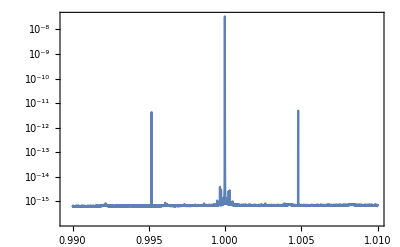

```mathematica
ListLogPlot[alphaCal,PlotRange->Full,Joined->True,defaultPlotFrameOptions]
```

```mathematica
hetBGLev=10^11(*normalization level, particular value is not important*);
hetPeakThresh=1 10^-13(*min amplitude for peak search*);
hetPeakThreshNorm=hetPeakThresh*hetBGLev;
```

```mathematica
(*find the heterodyne peaks and their positions*)
hetPeakList=Sort[XYFindPeaks[YScale[alphaCal,hetBGLev],0,0,hetPeakThreshNorm],#1[[2]]>#2[[2]]&][[;;3]]
```

{{9.99979×10^7,3337.24},{1.00478×10^8,0.492562},{9.95177×10^7,0.428139}}

```mathematica
calToneν=(Max[hetPeakList[[;;,1]]]-Min[hetPeakList[[;;,1]]])/2(*calibration tone frequency, Hz*)
```

480192.

```mathematica
ΔνHetInt=3. 10^3;(*Hz*)
```

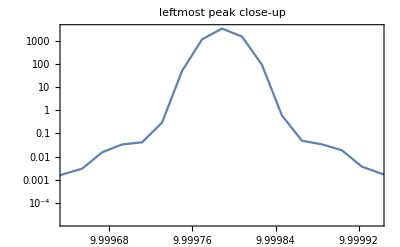

```mathematica
ListLogPlot[ScaleY[alphaCal,hetBGLev],PlotRange->{{hetPeakList[[1,1]]-ΔνHetInt/2,hetPeakList[[1,1]]+ΔνHetInt/2},Full},Joined->True,defaultPlotFrameOptions,PlotLabel->Style["leftmost peak close-up",Black]]
```

```mathematica
(*Integrated areas under the peaks*)
intList=Table[IntegrateXY[ScaleY[alphaCal,hetBGLev],{x[[1]]-ΔνHetInt/2,x[[1]]+ΔνHetInt/2}],{x,hetPeakList}]
intnList=Transpose[{{0,-1,1},intList/Mean[intList]}];
```

{1.17838×10^6,173.27,154.167}

Inferring the amplitude modulation coefficient α of the laser field defined according to the formula:

ⅇ^(-ⅈ ω_L t)+α/2 ⅇ^(-ⅈ (ω_L+Ω_M)t)+α/2 ⅇ^(-ⅈ (ω_L-Ω_M)t)

```mathematica
α=√(2(intList[[2]]+intList[[3]])/intList[[1]])
```

0.0235741

## Calibrated relative intensity noise spectra and noise vs power

```mathematica
calToneIntRng={457475.72815533984,469902.9126213593};
calToneInt=Table[IntegrateXY[tr,calToneIntRng],{tr,transmSpBbNoBg}];
```

```mathematica
rinSpBb=ScaleY[transmSpBbNoBg,2 α^2/calToneInt];
```

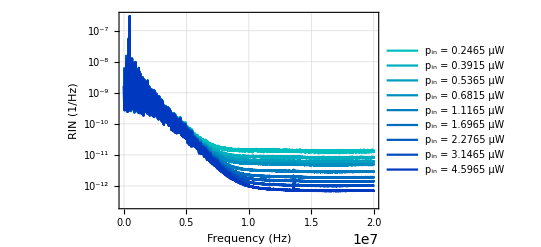

```mathematica
ListLogPlot[rinSpBb,
defaultPlotFrameOptions,
defaultPlotGridOptions,
Joined->True,
FrameLabel->{"Frequency (Hz)","RIN (1/Hz)"},
PlotStyle->Table[Directive[Thin,c],{c,BlueColors[Length[transmSpBbNoBg]]}](*BlueColors is one of the color themes defined in Utilities package for plotting sweeps like this one*),
ImageSize->400,
PlotLegends->Table["p_in = "~~ToString[p]~~" μW",{p,inPowList}]
]
```

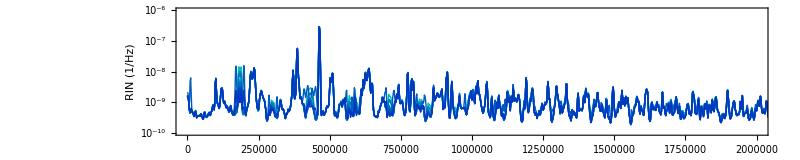

```mathematica
(* Low-frequency zoom into broadband spectrum *)
ListLogPlot[rinSpBb,
defaultPlotFrameOptions,
defaultPlotGridOptions,
Joined->True,
FrameLabel->{"Frequency (Hz)","RIN (1/Hz)"},
PlotStyle->Table[Directive[Thin,c],{c,BlueColors[Length[transmSpBbNoBg]]}],
ImageSize->800,
AspectRatio->1/5,
PlotRange->{{0,2 10^6},{10^-10,10^-6}}
]
```

```mathematica
(* Plotting RIN vs input power *)
rinIntBand={0.6 10^6,1.6 10^6};
rinLevInt=Table[{inPowList[[i]],IntegrateXY[rinSpBb[[i]],rinIntBand]/(rinIntBand[[2]]-rinIntBand[[1]])},{i,Length[rinSpBb]}];
```

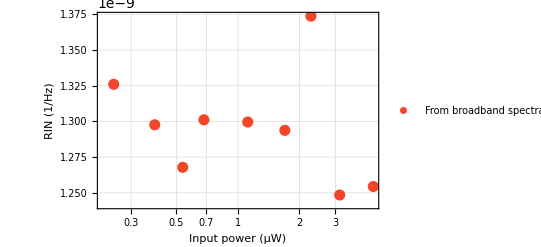

```mathematica
ListLogLinearPlot[{rinLevInt},
defaultPlotFrameOptions,
defaultPlotGridOptions,
PlotStyle->{Directive[redColors[[2]],PointSize[0.02]]},
FrameLabel->{"Input power (μW)","RIN (1/Hz)"},
ImageSize->400,
PlotLegends->{"From broadband spectra"}]
```